```mathematica
trainingData=Import["C:\\Users\\Honzaik\\la2_du\\ukol2\\train.csv"];
trainPol=trainingData[[All,2]]
trainToil=trainingData[[All,3]]
```

{40,40,39,38,40,34,34,32,35,32,33,38,32,33,35,35,31,36,35,40,45,47,47,48,55,58,59,59,65,77,100,44,32,39,38,38,33,25,27,37,39,40,37,41,40,39,40}

{11,11,11,11,10,10,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,11,11,12,27,17,13,12,13,12,12,13,13,14,14,13,12,14,13,13,13,13,12,14,20,12}

{45,47,47,48,55,58,59,59,65,77,100,44,32,39,38,38,33,25,27,37,39,40,37,41,40,39,40}

{{12,12,12,12,12,12,12,12,11,11,11,11,11,11,10,10,11,11,11,11},{12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,10,10,11,11,11},{12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,10,10,11,11},{11,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,10,10,11},{11,11,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,10,10},{12,11,11,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,10},{27,12,11,11,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11},{17,27,12,11,11,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11},{13,17,27,12,11,11,12,12,12,12,12,12,12,12,12,12,11,11,11,11},{12,13,17,27,12,11,11,12,12,12,12,12,12,12,12,12,12,11,11,11},{13,12,13,17,27,12,11,11,12,12,12,12,12,12,12,12,12,12,11,11},{12,13,12,13,17,27,12,11,11,12,12,12,12,12,12,12,12,12,12,11},{12,12,13,12,13,17,27,12,11,11,12,12,12,12,12,12,12,12,12,12},{13,12,12,13,12,13,17,27,12,11,11,12,12,12,12,12,12,12,12,12},{13,13,12,12,13,12,13,17,27,12,11,11,12,12,12,12,12,12,12,12},{14,13,13,12,12,13,12,13,17,27,12,11,11,12,12,12,12,12,12,12},{14,14,13,13,12,12,13,12,13,17,27,12,11,11,12,12,12,12,12,12},{13,14,14,13,13,12,12,13,12,13,17,27,12,11,11,12,12,12,12,12},{12,13,14,14,13,13,12,12,13,12,13,17,27,12,11,11,12,12,12,12},{14,12,13,14,14,13,13,12,12,13,12,13,17,27,12,11,11,12,12,12},{13,14,12,13,14,14,13,13,12,12,13,12,13,17,27,12,11,11,12,12},{13,13,14,12,13,14,14,13,13,12,12,13,12,13,17,27,12,11,11,12},{13,13,13,14,12,13,14,14,13,13,12,12,13,12,13,17,27,12,11,11},{13,13,13,13,14,12,13,14,14,13,13,12,12,13,12,13,17,27,12,11},{12,13,13,13,13,14,12,13,14,14,13,13,12,12,13,12,13,17,27,12},{14,12,13,13,13,13,14,12,13,14,14,13,13,12,12,13,12,13,17,27},{20,14,12,13,13,13,13,14,12,13,14,14,13,13,12,12,13,12,13,17}}

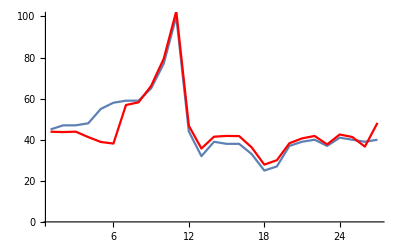

```mathematica
pocetVah=20;
b=trainPol[[pocetVah+1;;]]
A=Table[Table[trainToil[[i+j]],{j,pocetVah-1,0,-1}],{i,1,Length[b]}]
res=LeastSquares[A,b];
getEstimate[n_]:=res.Table[trainToil[[n-i]],{i,1,Length[res]}]
estimates=Table[getEstimate[i],{i,pocetVah+1,Length[trainPol]}];
gReal=ListLinePlot[trainPol[[pocetVah+1;;]],PlotRange->All];
gEst=ListLinePlot[estimates,PlotRange->All,PlotStyle->Red];
Show[gReal,gEst]
```

```mathematica
testData=Import["C:\\Users\\Honzaik\\la2_du\\ukol2\\test.csv"];
testToil=testData[[All,3]];
testPol=testData[[All,2]];
```

{1430329/966907,1748118/966907}

{1.47928,1.80795}

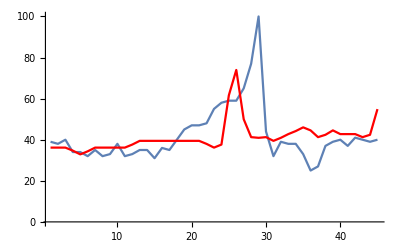

19.4665

89.9237

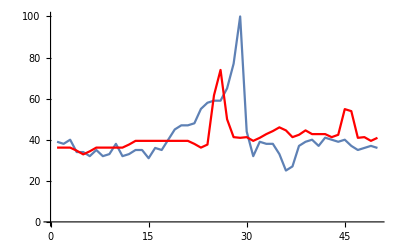

```mathematica
pocetVah=2;
startWeek=pocetVah+1;
b=trainPol[[startWeek;;]];
A=Table[Table[trainToil[[i+j]],{j,pocetVah-1,0,-1}],{i,1,Length[b]}];
res=LeastSquares[A,b]
N[res]
getEstimate[n_]:=res.Table[trainToil[[n-i]],{i,1,Length[res]}];
estimates=Table[getEstimate[i],{i,startWeek,Length[trainPol]}];
gReal=ListLinePlot[b,PlotRange->All];
gEst=ListLinePlot[estimates,PlotRange->All,PlotStyle->Red];
Show[gReal,gEst]
combinedToil=Join[trainToil,testToil];
getEstimate[n_]:=res.Table[combinedToil[[n-i]],{i,1,Length[res]}];
lReal=Join[trainPol,testPol][[startWeek;;]];
lEst=Table[getEstimate[i],{i,startWeek,Length[Join[trainPol,testPol]]}];
gReal=ListLinePlot[lReal,PlotRange->All];
gEst=ListLinePlot[lEst,PlotRange->All,PlotStyle->Red];
N[Norm[Take [(lReal-lEst),-Length[testPol]]]]
N[Norm[(lReal-lEst)]]
Show[gReal,gEst]
```

```mathematica
getError[n_]:=
Module[{},
pocetVah=n;
startWeek=pocetVah+1;
b=trainPol[[startWeek;;]];
A=Table[Table[trainToil[[i+j]],{j,pocetVah-1,0,-1}],{i,1,Length[b]}];
res=LeastSquares[A,b];
estimates=Table[res.Table[trainToil[[i-j]],{j,1,Length[res]}],{i,startWeek,Length[trainPol]}];
lReal=Join[trainPol,testPol][[startWeek;;]];
lEst=Table[res.Table[combinedToil[[i-j]],{j,1,Length[res]}],{i,startWeek,Length[Join[trainPol,testPol]]}];
{N[Norm[Take [(lReal-lEst),-Length[testPol]]]],
N[Norm[(lReal-lEst)]]}
]
```

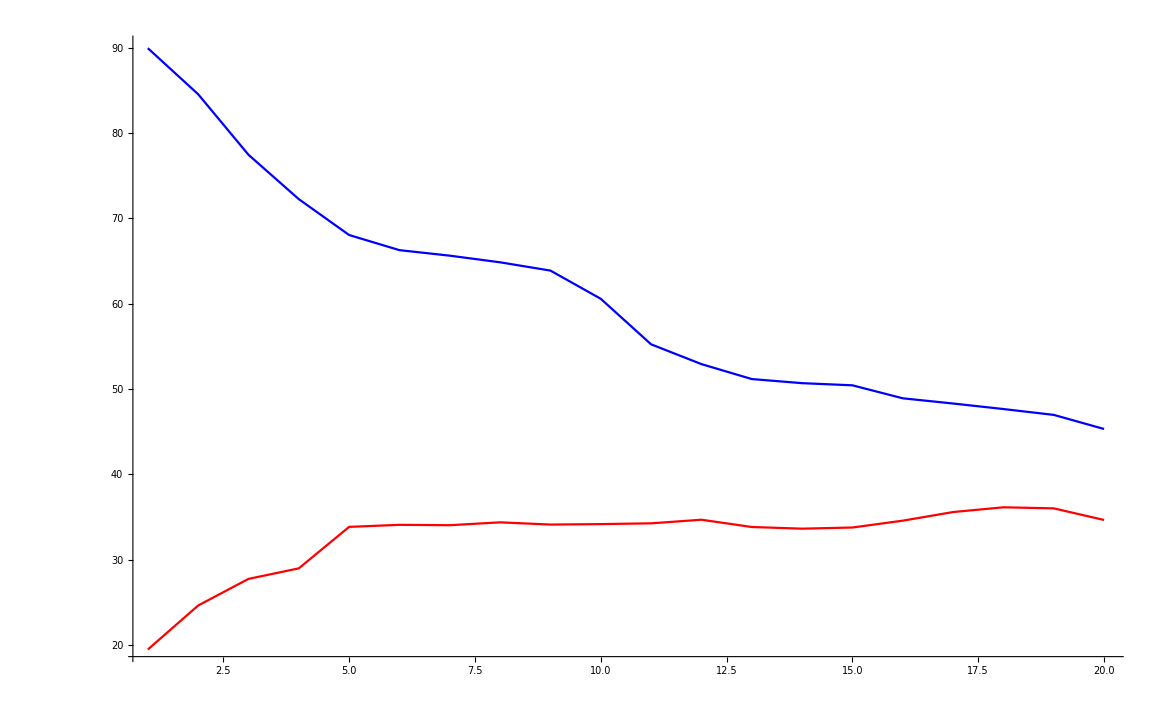

```mathematica
limit=21;
gTestError=ListLinePlot[Table[getError[i][[1]],{i,2,limit}],PlotRange->All,PlotStyle->Red];
gAllError=ListLinePlot[Table[getError[i][[2]],{i,2,limit}],PlotRange->All,PlotStyle->Blue];
Show[gTestError,gAllError,PlotRange->All]
```